```mathematica
FileNames["/home/carla/GDC/MUR/*.txt"]
```

{/home/carla/GDC/MUR/MUR_DOJ.txt,/home/carla/GDC/MUR/MUR_F.txt,/home/carla/GDC/MUR/MUR_Z.txt}

```mathematica
{"/home/carla/GDC/MUR/MUR_F.txt","/home/carla/GDC/MUR/MUR_F.txt","/home/carla/GDC/MUR/MUR_Z.txt"}
```

{/home/carla/GDC/MUR/MUR_F.txt,/home/carla/GDC/MUR/MUR_F.txt,/home/carla/GDC/MUR/MUR_Z.txt}

```mathematica
dataDLB=Map[Get[#]&, FileNames["/home/carla/GDC/DLB/*.txt"]][[2]]
dataMUR=Map[Get[#]&, FileNames["/home/carla/GDC/MUR/*.txt"]][[2]];
dataLYE=Map[Get[#]&, FileNames["/home/carla/GDC/LYE/*.txt"]][[2]];
dataPHI=Map[Get[#]&, FileNames["/home/carla/GDC/PHI/*.txt"]][[2]];
dataSED=Map[Get[#]&, FileNames["/home/carla/GDC/SED/*.txt"]][[2]];
dataAUS=Map[Get[#]&, FileNames["/home/carla/GDC/AUS/*.txt"]][[2]];
```

{{0,1},{0.5,1},{1,1},{1.5,1},{2,0.711231},{2.5,0.724184},{3,0.960851},{3.5,0.95858},{4,0.944457},{4.5,0.973095},{5,0.972236},{5.5,0.983254},{6,0.98879},{8,1}}

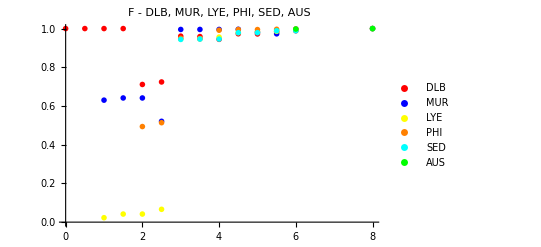

```mathematica
plotDMLPSA=ListPlot[{dataDLB,dataMUR, dataLYE, dataPHI, dataSED, dataAUS},PlotLegends->{"DLB","MUR","LYE", "PHI", "SED", "AUS"},PlotStyle->{Red,Blue,Yellow, Orange, Cyan, Green},PlotRange->All,PlotLabel->"F - DLB, MUR, LYE, PHI, SED, AUS",PlotMarkers->{{"D",12},{"M",12},{"L",12}, {"P",12},{"S",12},{"A",12}}]
```

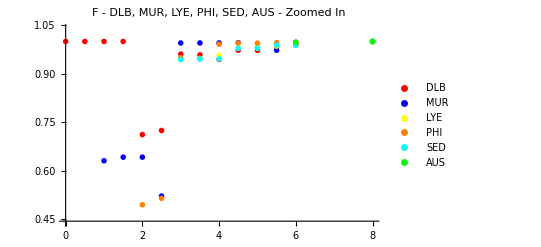

```mathematica
plotDMLPSAZoomedIn=ListPlot[{dataDLB,dataMUR, dataLYE, dataPHI, dataSED, dataAUS},PlotLegends->{"DLB","MUR","LYE", "PHI", "SED", "AUS"},PlotStyle->{Red,Blue,Yellow, Orange, Cyan, Green},PlotRange->{0.44,1.04},PlotLabel->"F - DLB, MUR, LYE, PHI, SED, AUS - Zoomed In",PlotMarkers->{{"D",12},{"M",12},{"L",12}, {"P",12},{"S",12},{"A",12}}]
```

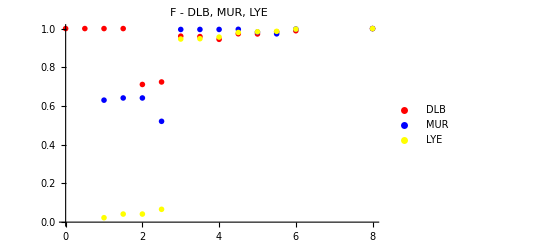

```mathematica
plotDML=ListPlot[{dataDLB,dataMUR, dataLYE},PlotLegends->{"DLB","MUR","LYE"},PlotStyle->{Red,Blue,Yellow},PlotRange->All,PlotLabel->"F - DLB, MUR, LYE",PlotMarkers->{{"D",12},{"M",12},{"L",12}}]
```

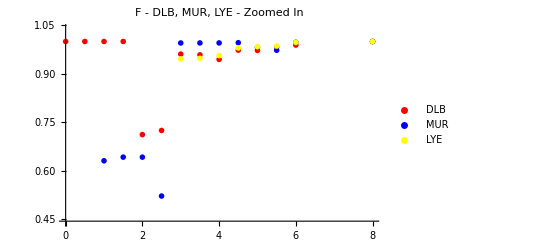

```mathematica
plotDMLZoomedIn=ListPlot[{dataDLB,dataMUR, dataLYE},PlotLegends->{"DLB","MUR","LYE"},PlotStyle->{Red,Blue,Yellow},PlotRange->{0.44,1.04},PlotLabel->"F - DLB, MUR, LYE - Zoomed In",PlotMarkers->{{"D",12},{"M",12},{"L",12}}]
```

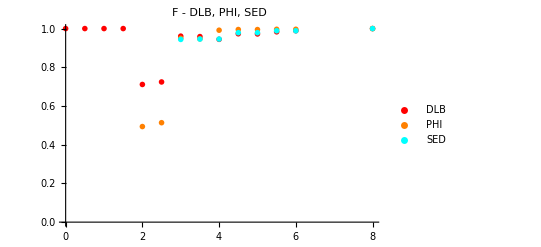

```mathematica
plotDPS=ListPlot[{dataDLB, dataPHI, dataSED},PlotLegends->{"DLB","PHI", "SED"},PlotStyle->{Red,Orange,Cyan},PlotRange->All,PlotLabel->"F - DLB, PHI, SED",PlotMarkers->{{"D",12},{"P",12},{"S",12}}]
```

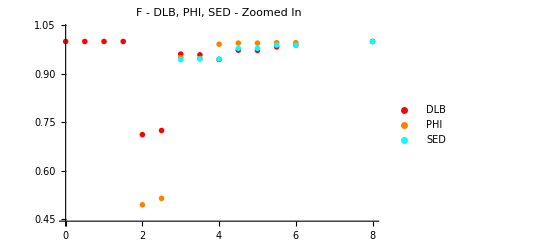

```mathematica
plotDPSZoomedIn=ListPlot[{dataDLB, dataPHI, dataSED},PlotLegends->{"DLB","PHI", "SED"},PlotStyle->{Red,Orange,Cyan},PlotRange->{0.44,1.04},PlotLabel->"F - DLB, PHI, SED - Zoomed In",PlotMarkers->{{"D",12},{"P",12},{"S",12}}]
```

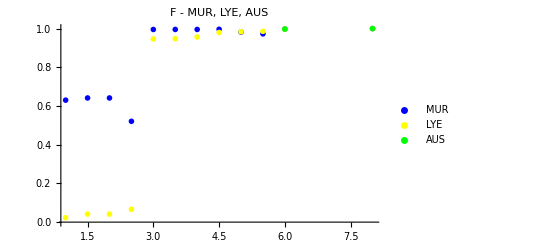

```mathematica
plotMLA=ListPlot[{dataMUR, dataLYE, dataAUS},PlotLegends->{"MUR","LYE", "AUS"},PlotStyle->{Blue,Yellow, Green},PlotRange->All,PlotLabel->"F - MUR, LYE, AUS",PlotMarkers->{{"M",12},{"L",12},{"A",12}}]
```

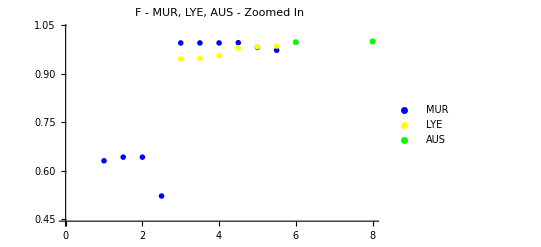

```mathematica
plotMLAZoomedIn=ListPlot[{dataMUR, dataLYE, dataAUS},PlotLegends->{"MUR","LYE", "AUS"},PlotStyle->{Blue,Yellow, Green},PlotRange->{0.44,1.04},PlotLabel->"F - MUR, LYE, AUS - Zoomed In",PlotMarkers->{{"M",12},{"L",12},{"A",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/ALL_PERS/F"];
Put[<|"DLB"->dataDLB,"MUR"->dataMUR,"LYE"->dataLYE, "PHI"->dataPHI,"SED"->dataSED,"AUS"->dataAUS|>,"F.txt"]
Export["F_DMLPSA.jpeg",plotDMLPSA,ImageSize->850]
Export["F_DMLPSA_ZoomedIn.jpeg",plotDMLPSAZoomedIn,ImageSize->850]
Export["F_DML.jpeg",plotDML,ImageSize->850]
Export["F_DML_ZoomedIn.jpeg",plotDMLZoomedIn,ImageSize->850]
Export["F_DPS.jpeg",plotDPS,ImageSize->850]
Export["F_DPS_ZoomedIn.jpeg",plotDPSZoomedIn,ImageSize->850]
Export["F_MLA.jpeg",plotMLA,ImageSize->850]
Export["F_MLA_ZoomedIn.jpeg",plotMLAZoomedIn,ImageSize->850]
```

F_DMLPSA.jpeg

F_DMLPSA_ZoomedIn.jpeg

F_DML.jpeg

F_DML_ZoomedIn.jpeg

F_DPS.jpeg

F_DPS_ZoomedIn.jpeg

F_MLA.jpeg

F_MLA_ZoomedIn.jpeg